Automatic unit conversion >

# Working with units

The AutomaticUnits package provides capabilities for working with phyisical quantities associated with various units.

Its aim is to automate both the conversions between different unit values and also to ensure dimensional compatibilitity.

Over 1000 different units are supported.

Load the units package first.

```mathematica
<<AutomaticUnits`
```

Calculations involving units will automatically convert arguments into a suitable common default unit. In most cases the default is SI units.

```mathematica
10.5Meter+14 Inch
```

10.8556 Meter

No conversion will be performed if quantities are already in a common unit system

```mathematica
37 Yard+12 Yard
```

49 Yard

Where input units are not dimensionally compatible, no computation will be performed.

```mathematica
Day + Inch
```

Unit::incomp1: Units DayInch are not compatible

Day+Inch

Composite units can be used by multiplying powers of units, and will also be handled automatically.

```mathematica
2.5 Atmosphere Acre+4*10^7 KilogramMeter Second^-2
```

1.06512×10^9 Newton

SimplifyUnits will try to find simpler equivelents to composite units.

```mathematica
SimplifyUnits[0.1 Atmosphere Acre]
```

4.10048×10^7 Newton

Most operators, for which unit based quanties make sense, will automatically handle units.

```mathematica
2000 Meter>1.2 Mile
```

True

```mathematica
Sort[{Foot, Inch, Mile, 200 Yard}]
```

{Inch,Foot,200 Yard,Mile}

```mathematica
Max[{Foot, Inch, Mile, 200 Yard}]
```

Mile

```mathematica
Solve[30 x+200 Meter==100.Foot,x]
```

{{x→-5.65067 Meter}}

```mathematica
Reduce[30 x+200 Meter==100.Foot,x]
```

x==-5.65067 Meter

Some data constructors can support ranges or intervals using unit based quanties. For example, here we generate 10 random quantities between 1 Yard and 1 Meter...

```mathematica
RandomReal[{Yard,Meter},{10}]
```

{0.985323 Meter,0.966027 Meter,0.988901 Meter,0.922013 Meter,0.967322 Meter,0.98416 Meter,0.958199 Meter,0.942732 Meter,0.933565 Meter,0.938031 Meter}

```mathematica
Range[10 Meter]
```

{Meter,2 Meter,3 Meter,4 Meter,5 Meter,6 Meter,7 Meter,8 Meter,9 Meter,10 Meter}

Or generate values beween 10 Meters and 13 Yards in 1 Foot steps.

```mathematica
Range[10. Meter, 13 Yard, Foot]
```

{10. Meter,10.3048 Meter,10.6096 Meter,10.9144 Meter,11.2192 Meter,11.524 Meter,11.8288 Meter}

Many plotting routines will handle units, and will usually display the resulting units as AxesLabels.

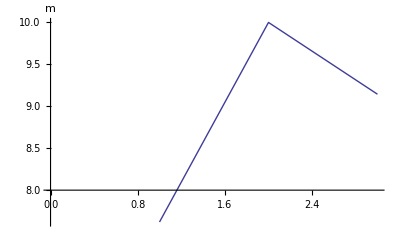

```mathematica
ListLinePlot[{300 Inch,10 Meter,10 Yard}]
```

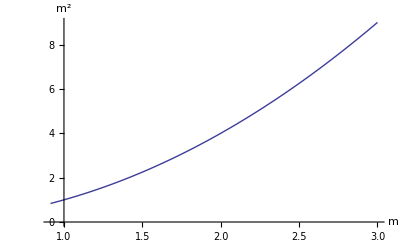

```mathematica
Plot[x^2,{x,3 Foot, 3 Meter}]
```

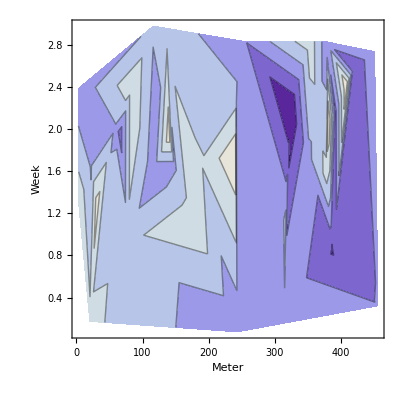

```mathematica
data=Transpose[{
RandomReal[{3. Foot,500 Yard},{40}],
RandomReal[3 Week,{40}],
RandomReal[3 Farad,{40}]}];
ListContourPlot[data]
```

Angles are considered to have an angle dimension and so, for example Steredian is not dimensionally equivelent to Radian. Angle units are handled automatically by trigonometric functions

```mathematica
Sin[RightAngle/3.]
```

0.5

```mathematica
Cos[Sqrt[2. Steradian]]
```

0.155944

Unit based quantities have a head Unit which is not shown in StandardForm.

```mathematica
FullForm[10 Meter]
```

Unit[10,"Meter"]

In TraditionalForm, traditional short labels, with tooltips, are used for the units.

```mathematica
TraditionalForm[10 Meter]
```

10 m

You can convert quantities to specific units

```mathematica
Convert[Meter,Furlong]
```

125/25146 Furlong

Or to appropriate the most appropriate unit from a list

```mathematica
Convert[1.Meter,{Yard,Mile,Day}]
```

1.09361 Yard

```mathematica
Convert[2000.Meter,{Yard,Mile,Day}]
```

1.24274 Mile

A large collection of predefined sets of units is available

```mathematica
Convert[100.Kilogram,"Imperial"]
```

1.96841 Hundredweight

```mathematica
Convert[100.Kilogram,"Atomic"]
```

1.09777×10^32 ElectronRestMass

The available named unit sets is given by...

```mathematica
UnitSet[]
```

{All,Alternative,AlternativeNames,Anthropic,Arabic,Astronomical,Atomic,Avoirdupois,BritishAvoirdupois,CGS,Champagne,IEC,Imperial,InteractiveChoices,Japanese,Malay,Maltese,MeterTonneSecond,MKS,Norwegian,Planck,PrefixedSI,Roman,Russian,Scottish,SI,Spanish,Survey,Swedish,Taiwanese,Troy,USCustomary}

You can see or change the members of a particular set or create new sets.

```mathematica
UnitSet["Troy"]
```

{Grain,TroyOunce,TroyPound,Pennyweight}

```mathematica
Convert[0.1 Gram,"Troy"]
```

1.54324 Grain

```mathematica
UnitSet["HeavyTroy"] = {Unit[1, "TroyOunce"], Unit[1, "TroyPound"], Unit[1, "Pennyweight"]};
Convert[0.1 Gram, "HeavyTroy"]
```

0.0643015 Pennyweight

You can declare new units

```mathematica
DeclareUnit["word"];
DeclareUnit["page",2000 word];
DeclareUnit["book",200 page];
book +200 word
```

400200 word

```mathematica
Convert[book +2000 word, page]
```

201 page

Temperatures are assumed to represent temperature differences for standard unit conversion

```mathematica
Celsius/Meter+Fahrenheit/Meter
```

14/9 Kelvin Meter^-1

But their different origins are respected using ConvertTemperature

```mathematica
ConvertTemperature[122.01 Celsius,Fahrenheit]
```

251.618 Fahrenheit